{{y1→InterpolatingFunction[{{0.,0.}},<>],y2→InterpolatingFunction[{{0.,0.}},<>]}}

InterpolatingFunction[{{0.,0.}},<>][t]

InterpolatingFunction[{{0.,0.}},<>][t]

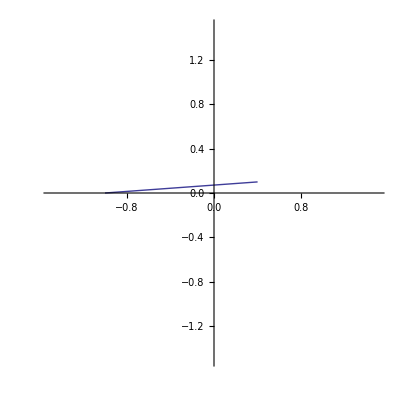

{{y1→InterpolatingFunction[{{1.,100.}},<>],y2→InterpolatingFunction[{{1.,100.}},<>]}}

InterpolatingFunction[{{1.,100.}},<>][t]

InterpolatingFunction[{{1.,100.}},<>][t]

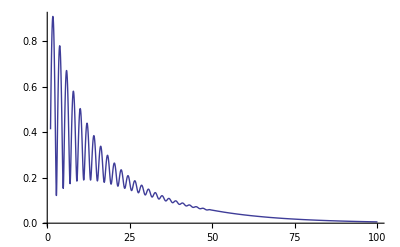

{0.908078,{t→1.71229}}

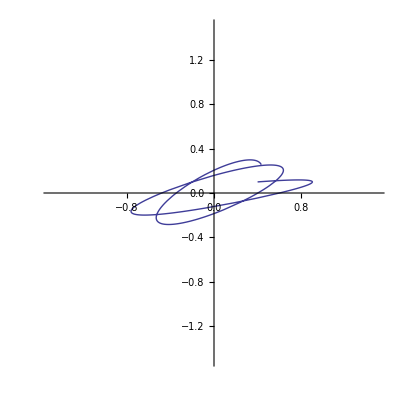

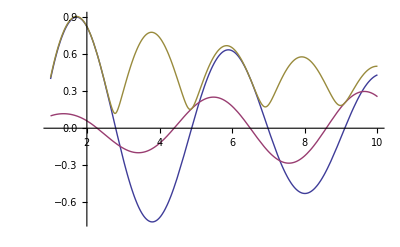

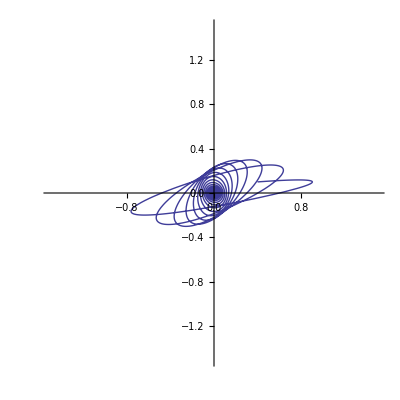

```mathematica
β=-1.4;
h=1;
tm =100;
ω=0.1;
y[t_]=({{y1[t]}, {y2[t]}});
B = ({{β, ω}, {-ω, β}});
init=y[0]=={{-1},{0}};
sol=NDSolve[N[LogicalExpand[y'[t]==B.y[t-t]&&init]],{y1,y2},{t,0,h}]
yy1[t_]=y1[t]/.sol[[1]]
yy2[t_]=y2[t]/.sol[[1]]

ParametricPlot[{yy1[t],yy2[t]},{t,0,h},PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
sol=NDSolve[{LogicalExpand[y'[t]==B.y[t-h]],y1[t /; t≤h]==yy1[t],y2[t /; t≤h]==yy2[t]},{y1,y2},{t,h,tm}]
yy1[t_]=y1[t]/.sol[[1]]
yy2[t_]=(y2[t]/.sol[[1]])
Plot[{ √(yy1[t]^2+yy2[t]^2)},{t,h,tm},PlotRange->Full]
FindMaximum[{√(yy1[t]^2+yy2[t]^2)&&h≤ t≤ tm},{t,h}]
ParametricPlot[{(y1[t]/.sol[[1]]),(y2[t]/.sol[[1]])},{t,h,10},PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
Plot[{yy1[t],yy2[t], √(yy1[t]^2+yy2[t]^2)},{t,h,10},PlotRange->Full]
ParametricPlot[{(y1[t]/.sol[[1]]),(y2[t]/.sol[[1]])},{t,h,tm},PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```